```mathematica
StringSplit[#,"_"]&@First@fnames
```

{C:\Users\Clint\Google Drive\- Programming\Mathematica\Machine Learing\Final Project Hamed\RNR4061\Clint\DimensionReduction\Results\Results,2Class,CNN,Ademxapp Model A.csv}

```mathematica
fnames=FileNames["*.csv",FileNameJoin[{NotebookDirectory[],"Results"}]];
extractedResultsAssocs=Join[
AssociationThread[First@#->Transpose@Rest@#]&@Import@#,
<|"class"->#[[-3]],"type"->#[[-2]],"model"->StringTake[#[[-1]],{1,-5}]|>&@StringSplit[#,"_"]&@#
]&/@fnames;

extractedResultsAssocs=Join[#,
<|"all_test_macroAvgAccuracy"->(
(CMMacroAvgACC/@ToExpression[StringReplace[#,{"["->"{","]"->"}"}]])&/@#["Confusion Matrix"])|>
]&/@extractedResultsAssocs;
extractedResultsAssocs=Join[#,
<|
"mean_test_macroAvgAccuracy"->Mean/@#["all_test_macroAvgAccuracy"],
"med_test_macroAvgAccuracy"->Median/@#["all_test_macroAvgAccuracy"]
|>
]&/@extractedResultsAssocs;
```

```mathematica
listArgMax[a_]:=Position[a,Max[a]]⟦1,1⟧
```

#### CLFMetrics

```mathematica
Clear[ROCAssociationQ];
ROCAssociationQ[ obj_ ] :=
    AssociationQ[obj] &&
        Length[Intersection[Keys[obj], {"TruePositive", "FalsePositive", "TrueNegative", "FalseNegative"}]] == 4;

TPR[rocAssoc_?ROCAssociationQ] := (rocAssoc["TruePositive"]) / (rocAssoc["TruePositive"] + rocAssoc["FalseNegative"]);
TPR[rocs : ({_?ROCAssociationQ..} | <|_?ROCAssociationQ..|> )] := Map[TPR, rocs];
SPC[rocAssoc_?ROCAssociationQ] := (rocAssoc["TrueNegative"]) / (rocAssoc["FalsePositive"] + rocAssoc["TrueNegative"]);
SPC[rocs : ({_?ROCAssociationQ..} | <|_?ROCAssociationQ..|> )] := Map[SPC, rocs];
PPV[rocAssoc_?ROCAssociationQ] := (rocAssoc["TruePositive"]) / (rocAssoc["TruePositive"] + rocAssoc["FalsePositive"]);
PPV[rocs : ({_?ROCAssociationQ..} | <|_?ROCAssociationQ..|> )] := Map[PPV, rocs];
NPV[rocAssoc_?ROCAssociationQ] := (rocAssoc["TrueNegative"]) / (rocAssoc["TrueNegative"] + rocAssoc["FalseNegative"]);
NPV[rocs : ({_?ROCAssociationQ..} | <|_?ROCAssociationQ..|> )] := Map[NPV, rocs];
FPR[rocAssoc_?ROCAssociationQ] := (rocAssoc["FalsePositive"]) / (rocAssoc["FalsePositive"] + rocAssoc["TrueNegative"]);
FPR[rocs : ({_?ROCAssociationQ..} | <|_?ROCAssociationQ..|> )] := Map[FPR, rocs];
FDR[rocAssoc_?ROCAssociationQ] := (rocAssoc["FalsePositive"]) / (rocAssoc["FalsePositive"] + rocAssoc["TruePositive"]);
FDR[rocs : ({_?ROCAssociationQ..} | <|_?ROCAssociationQ..|> )] := Map[FDR, rocs];
FNR[rocAssoc_?ROCAssociationQ] := (rocAssoc["FalseNegative"]) / (rocAssoc["FalseNegative"] + rocAssoc["TruePositive"]);
FNR[rocs : ({_?ROCAssociationQ..} | <|_?ROCAssociationQ..|> )] := Map[FNR, rocs];
ACC[rocAssoc_?ROCAssociationQ] := (rocAssoc["TruePositive"] + rocAssoc["TrueNegative"]) / Total[Values[rocAssoc]];
ACC[rocs : ({_?ROCAssociationQ..} | <|_?ROCAssociationQ..|> )] := Map[ACC, rocs];
FOR[rocAssoc_?ROCAssociationQ] := 1 - NPV[rocAssoc];
FOR[rocs : ({_?ROCAssociationQ..} | <|_?ROCAssociationQ..|> )] := Map[FOR, rocs];
F1[rocAssoc_?ROCAssociationQ] := 2 * PPV[rocAssoc] * TPR[rocAssoc] / ( PPV[rocAssoc] + TPR[rocAssoc] );
F1[rocs : ({_?ROCAssociationQ..} | <|_?ROCAssociationQ..|> )] := Map[F1, rocs];
```

```mathematica
CMCndReduce[cm_,cnd_]:=Module[{tp,tn,fn,fp},
tp=cm[[cnd,cnd]];
fn=Total@cm[[cnd,;;]]-tp;
fp=Total@Transpose@cm[[;;,cnd]]-tp;
tn=Total@Total@cm-(tp+fn+fn+fp);
AssociationThread[
{"TruePositive", "FalsePositive", "TrueNegative", "FalseNegative"}->{tp,fp,tn,fn}]
]
CMMacroAvgACC[cm_]:=Total@Table[ACC[CMCndReduce[N@cm,i]],{i,Length@cm}]/Length@cm
```

## Tables

```mathematica
cms=extractedResultsAssocs[[1]]["Confusion Matrix"];
macroAvgAccs=(CMMacroAvgACC/@ToExpression[StringReplace[#,{"["->"{","]"->"}"}]])&/@cms;
meanMacroAvgAccs=Mean/@macroAvgAccs;
```

```mathematica
largeList=Module[{maxAcIdx=listArgMax[#["avg_test_accuracy"]]},{
#["model"],
#["Model"]⟦maxAcIdx⟧
}]&/@Select[extractedResultsAssocs,#class=="5Class"&];
DeleteDuplicates@Flatten@largeList
```

{EfficientNet,MLPClassifier,Inception V1,RandomForestClassifier,Inception V3,ResNet-101,ResNet-152,GradientBoostingClassifier,ResNet-50,SE-Inception-BatchNorm,SE-ResNet-101,SE-ResNet-50,SE-ResNeXt-101,Squeeze-and-Excitation Net,SqueezeNet V1.1,VGG-16,VGG-19,Wide ResNet-50-2,Hadamard,LatentSemanticAnalysis,LLE,VotingClassifier,MultidimensionalScaling,PrincipalComponentsAnalysis,TSNE}

```mathematica
abrvAssoc=StringReplace[#,{
"Ademxapp Model A"->"AM A?","RandomForestClassifier"->"RFC","EfficientNet"->"EN","MLPClassifier"->"MLP","Inception"->"IN","GradientBoostingClassifier"->"GB","ResNet"->"RN","Wide ResNet-50-2"->"wRN-50-2","BatchNorm"->"BN","ResNet-101"->"RN-101","SE-ResNeXt"->"SE-RNX","ResNet-152"->"RN-152","Squeeze-and-Excitation Net"->"SEN-154","SqueezeNet V1.1"->"SN","VGG-16"->"VGG-16","VGG-19"->"VGG-19","Hadamard"->"H","LatentSemanticAnalysis"->"LSA","LLE"->"LLE","VotingClassifier"->"VC","MultidimensionalScaling"->"MS","PrincipalComponentsAnalysis"->"PCA","LogisticRegression"->"LR","TSNE"->"TSNE","LinearSVC"->"lSVC","KNeighborsClassifier"->"KNN","AdaBoostClassifier"->"AB","GaussianNB"->"gNB","LogisticRegression"->"LR","MobileNet"->"MN"}]&;
```

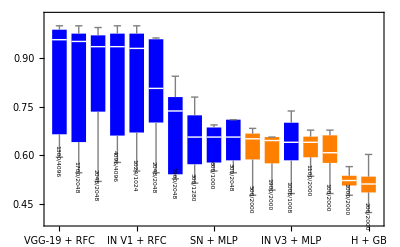

```mathematica
largeList=Module[{maxAcIdx=listArgMax[#["avg_test_accuracy"]]},{
#["type"],
#["model"],
StringReplace[#["all_test_accuracy"]⟦maxAcIdx⟧,{"["->"{","]"->"}"}]//ToExpression,
#["Model"]⟦maxAcIdx⟧,
#["Selected"]⟦maxAcIdx⟧,
Max[#["Selected"]]
}]&/@Select[extractedResultsAssocs,#class=="5Class"&];
largeList=SortBy[largeList,-Median[#[[3]]]&];
BoxWhiskerChart[largeList[[;;,3]],"Median",
ChartLabels->Placed[
{
Map[Rotate[#,-π/2]&,
abrvAssoc[#1]<>" + "<>abrvAssoc[#2]&@@@({largeList[[;;,2]],largeList[[;;,4]]}ᵀ)
,{-1}],
Map[Rotate[Style[#,6],-π/2]&,
ToString[#1]<>"/"<>ToString[#2]&@@@({largeList[[;;,5]],largeList[[;;,6]]}ᵀ)
,{-1}]
}
,{Axis,Below}],
ChartStyle->(If[#==="stat",Orange,Blue]&/@largeList[[;;,1]])]
```

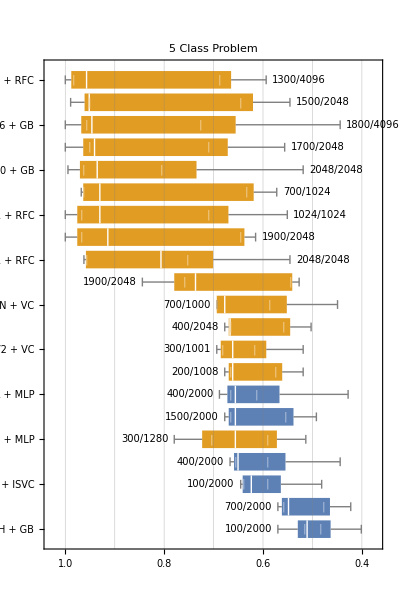

```mathematica
largeList=Module[{maxAcIdx=listArgMax[#["med_test_accuracy"]]},{
#["type"],
#["model"],
StringReplace[#["all_test_accuracy"]⟦maxAcIdx⟧,{"["->"{","]"->"}"}]//ToExpression,
#["Model"]⟦maxAcIdx⟧,
#["Selected"]⟦maxAcIdx⟧,
Max[#["Selected"]]
}]&/@Select[extractedResultsAssocs,#class=="5Class"&];
largeList=SortBy[largeList,Median[#[[3]]]&];
sty=Directive[Black,10];
fiveStageResults=BoxWhiskerChart[largeList[[;;,3]],"Median",
ChartLabels->Placed[
{
abrvAssoc[#1]<>" + "<>abrvAssoc[#2]&@@@({largeList[[;;,2]],largeList[[;;,4]]}ᵀ),
If[Median[#3]>.8,Style[ToString[#1]<>"/"<>ToString[#2],Background->White],""]&@@@({largeList[[;;,5]],largeList[[;;,6]],largeList[[;;,3]]}ᵀ),
If[Median[#3]<=.8,Style[ToString[#1]<>"/"<>ToString[#2],Background->White],""]&@@@({largeList[[;;,5]],largeList[[;;,6]],largeList[[;;,3]]}ᵀ)
}
,{Axis,After,Before}],
ChartStyle->(If[#==="stat",RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051]]&/@largeList[[;;,1]]),
GridLines->{-Range[.3,1,0.1],None},PlotRange->{-{0.3,1},Automatic},PlotRangePadding->{None,Automatic},
PlotLabel->"5 Class Problem",FrameStyle->sty,LabelStyle->sty,
ChartBaseStyle->Directive[Thick(*, Opacity[0.25]*)]&/@largeList[[;;,1]],
BarOrigin->Right,AspectRatio->1.5];
fiveStageResults=Show[{
fiveStageResults,
(*Graphics[Table[Text[{i,j},{i,j}],{i,-10,10,1},{j,-10,10,1}]]*)
Graphics[
With[{textPos=Map[Append[#2],{-#}&/@#1[[3]]]},
(*Style[Text["x",#]&/@textPos,(*If[#1[[1]]==="stat",RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051]]*)Gray,8]*)
Style[Text["|",#]&/@Sort[textPos][[{2,4}]],12,If[#1[[1]]==="stat",Lighter@Lighter@RGBColor[0.368417, 0.506779, 0.709798],Lighter@Lighter@RGBColor[0.880722, 0.611041, 0.142051]],Bold]
(*{Style[Text["x",#]&/@Sort[textPos][[{2,4}]],10,If[#1[[1]]==="stat",Darker@Darker@RGBColor[0.368417, 0.506779, 0.709798],Darker@Darker@RGBColor[0.880722, 0.611041, 0.142051]],Bold],Style[Text["+",Mean@textPos],16,White,Bold]}*)
]&@@@({largeList,Range@Length@largeList}ᵀ)
]
}]
```

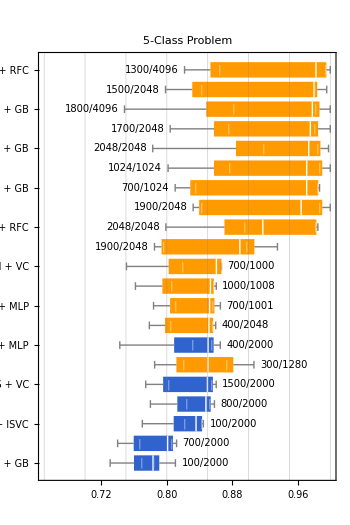

```mathematica
clr1=ColorData[112][2];clr2=ColorData[112][3];
largeList=Module[{maxAcIdx=listArgMax[#["med_test_macroAvgAccuracy"]]},{
#["type"],
#["model"],
(*StringReplace[#["all_test_macroAvgAccuracy"]⟦maxAcIdx⟧,{"["->"{","]"->"}"}]//ToExpression*)
#["all_test_macroAvgAccuracy"]⟦maxAcIdx⟧,
#["Model"]⟦maxAcIdx⟧,
#["Selected"]⟦maxAcIdx⟧,
Max[#["Selected"]]
}]&/@Select[extractedResultsAssocs,#class=="5Class"&];
largeList=SortBy[largeList,Median[#[[3]]]&];
largeList5Class=largeList;
sty=Directive[Black,10];
fiveStageResults=BoxWhiskerChart[largeList[[;;,3]],"Median",
ChartLabels->Placed[
{
abrvAssoc[#1]<>" + "<>abrvAssoc[#2]&@@@({largeList[[;;,2]],largeList[[;;,4]]}ᵀ),
If[Max[#3]>.93,Style[ToString[#1]<>"/"<>ToString[#2],Background->White],""]&@@@({largeList[[;;,5]],largeList[[;;,6]],largeList[[;;,3]]}ᵀ),
If[Max[#3]<=.93,Style[ToString[#1]<>"/"<>ToString[#2],Background->White],""]&@@@({largeList[[;;,5]],largeList[[;;,6]],largeList[[;;,3]]}ᵀ)
}
,{Axis,Before,After}],
ChartStyle->(If[#==="stat",clr1,clr2]&/@largeList[[;;,1]]),
GridLines->{Range[.3,1,0.05],None},PlotRange->{{0.65,1},Automatic},PlotRangePadding->{None,Automatic},
PlotLabel->"5-Class Problem",FrameStyle->sty,LabelStyle->sty,
ChartBaseStyle->Directive[Thick(*, Opacity[0.25]*)]&/@largeList[[;;,1]],
BarOrigin->Left,AspectRatio->1.5];
fiveStageResults=Show[{
fiveStageResults,
(*Graphics[Table[Text[{i,j},{i,j}],{i,-10,10,1},{j,-10,10,1}]]*)
Graphics[
With[{textPos=Map[Append[#2],{#}&/@#1[[3]]]},
(*Style[Text["x",#]&/@textPos,(*If[#1[[1]]==="stat",RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051]]*)Gray,8]*)
Style[Text["|",#]&/@Sort[textPos][[{2,4}]],9,If[#1[[1]]==="stat",Lighter@Lighter@clr1,Lighter@Lighter@clr2],Bold]
(*{Style[Text["x",#]&/@Sort[textPos][[{2,4}]],10,If[#1[[1]]==="stat",Darker@Darker@RGBColor[0.368417, 0.506779, 0.709798],Darker@Darker@RGBColor[0.880722, 0.611041, 0.142051]],Bold],Style[Text["+",Mean@textPos],16,White,Bold]}*)
]&@@@({largeList,Range@Length@largeList}ᵀ)
]
},ImageSize->350]
```

```mathematica
trad5ClassScores=Association[(If[#[[1]]!="stat",#[[2]]->Median[#[[3]]]])&/@largeList/.Null->Sequence[]]
tran5ClassScores=KeyDrop[Association[KeyValueMap[#1[[1]]->#2["Value"]&,accuracies5ClassAssoc]],{"MobileNet V2","SE-ResNet-50"}]
Table[trad5ClassScores[k]-tran5ClassScores[k],{k,Keys@tran5ClassScores}]
```

<|EfficientNet→0.850294,Wide ResNet-50-2→0.851529,MobileNet V2→0.852384,Inception V3→0.85336,SqueezeNet V1.1→0.860673,ResNet-152→0.889396,ResNet-101→0.917458,SE-ResNeXt-101→0.964343,SE-Inception-BatchNorm→0.971125,Inception V1→0.971147,ResNet-50→0.973613,SE-ResNet-101→0.975601,VGG-16→0.978092,Squeeze-and-Excitation Net→0.980153,VGG-19→0.982496|>

<|EfficientNet→0.871583,Inception V1→0.895354,Inception V3→0.895611,ResNet-101→0.895425,ResNet-152→0.890727,ResNet-50→0.897846,SE-Inception-BatchNorm→0.890586,SE-ResNet-101→0.893359,SE-ResNeXt-101→0.890624,Squeeze-and-Excitation Net→0.880956,SqueezeNet V1.1→0.864321,VGG-16→0.893552,VGG-19→0.886393,Wide ResNet-50-2→0.8981|>

{-0.0212895,0.0757935,-0.0422511,0.0220331,-0.00133122,0.075767,0.0805393,0.0822418,0.0737182,0.0991975,-0.00364735,0.0845403,0.0961021,-0.0465708}

```mathematica
Mean@%386
```

0.054734

```mathematica
(*■*)
```

```mathematica
ColorData
```

```mathematica
ColorData[96]
```

```mathematica
ColorData[97]/@Range[6]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387]}

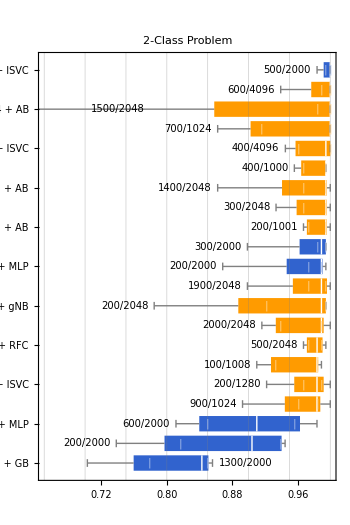

```mathematica
clr1=ColorData[112][2];clr2=ColorData[112][3];
largeList=Module[{maxAcIdx=listArgMax[#["med_test_macroAvgAccuracy"]]},{
#["type"],
#["model"],
(*StringReplace[#["all_test_macroAvgAccuracy"]⟦maxAcIdx⟧,{"["->"{","]"->"}"}]//ToExpression*)
#["all_test_macroAvgAccuracy"]⟦maxAcIdx⟧,
#["Model"]⟦maxAcIdx⟧,
#["Selected"]⟦maxAcIdx⟧,
Max[#["Selected"]]
}]&/@Select[extractedResultsAssocs,#class=="2Class"&];
largeList=SortBy[largeList,Median[#[[3]]]&];
largeList2Class=largeList;
sty=Directive[Black,10];
twoStageResults=BoxWhiskerChart[largeList[[;;,3]],"Median",
ChartLabels->Placed[
{
abrvAssoc[#1]<>" + "<>abrvAssoc[#2]&@@@({largeList[[;;,2]],largeList[[;;,4]]}ᵀ),
If[Median[#3]>.86&&Min[#3]>.7,Style[ToString[#1]<>"/"<>ToString[#2],Background->White],""]&@@@({largeList[[;;,5]],largeList[[;;,6]],largeList[[;;,3]]}ᵀ),
If[Median[#3]>.86&&Min[#3]<.7,Style[ToString[#1]<>"/"<>ToString[#2],Background->White],""]&@@@({largeList[[;;,5]],largeList[[;;,6]],largeList[[;;,3]]}ᵀ),
If[Median[#3]<=.86,Style[ToString[#1]<>"/"<>ToString[#2],Background->White],""]&@@@({largeList[[;;,5]],largeList[[;;,6]],largeList[[;;,3]]}ᵀ)
}
,{Axis,Before,Center,After}],
ChartStyle->(If[#==="stat",clr1,clr2]&/@largeList[[;;,1]]),
GridLines->{Range[.3,1,0.05],None},PlotRange->{{0.65,1},Automatic},PlotRangeClipping->True,PlotRangePadding->{None,Automatic},
PlotLabel->"2-Class Problem",FrameStyle->sty,LabelStyle->sty,
BarOrigin->Left,AspectRatio->1.5];
twoStageResults=Show[{
twoStageResults,
(*Graphics[Table[Text[{i,j},{i,j}],{i,-10,10,1},{j,-10,10,1}]]*)
Graphics[
With[{textPos=Map[Append[#2],{#}&/@#1[[3]]]},
(*Style[Text["x",#]&/@textPos,(*If[#1[[1]]==="stat",clr1,clr2]*)Gray,8]*)
Style[Text["|",#]&/@Sort[textPos][[{2,4}]],12,If[#1[[1]]==="stat",Lighter@Lighter@clr1,Lighter@Lighter@clr2],Bold]
(*{Style[Text["x",#]&/@Sort[textPos][[{2,4}]],10,If[#1[[1]]==="stat",Darker@Darker@RGBColor[0.368417, 0.506779, 0.709798],Darker@Darker@RGBColor[0.880722, 0.611041, 0.142051]],Bold],Style[Text["+",Mean@textPos],16,White,Bold]}*)
]&@@@({largeList,Range@Length@largeList}ᵀ)
]
},ImageSize->350]
```

```mathematica
Select[largeList,Median[#[[3]]]>.99&][[;;,{1,2}]];
Length@%
%%//TableForm
```

8

CNN | ResNet-152
CNN | SE-ResNet-101
CNN | SqueezeNet V1.1
CNN | VGG-16
CNN | SE-Inception-BatchNorm
CNN | Squeeze-and-Excitation Net
CNN | VGG-19
stat | LLE

```mathematica
Complement[Keys@tran5ClassScores,Keys@trad5ClassScores]
```

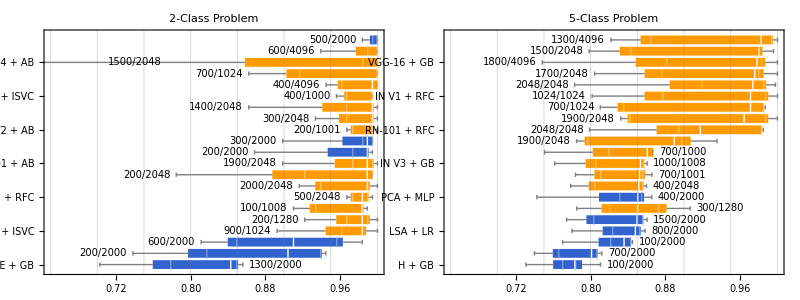

```mathematica
Grid[{{twoStageResults,fiveStageResults}},ImageSizeMultipliers->{1,1}]
```

```mathematica
Module[{maxAcIdx=listArgMax[#["avg_test_accuracy"]]},{
#["type"],
#["model"],
#["avg_test_accuracy"]⟦maxAcIdx⟧,
#["Model"]⟦maxAcIdx⟧,
#["Selected"]⟦maxAcIdx⟧
}]&/@Select[extractedResultsAssocs,#class=="2Class"&]//TableForm
```

CNN | Ademxapp Model A | 0.981778 | MLPClassifier | 1600
CNN | EfficientNet | 0.974268 | LinearSVC | 400
CNN | Inception V1 | 0.965701 | LinearSVC | 900
CNN | Inception V3 | 0.973164 | RandomForestClassifier | 400
CNN | ResNet-101 | 0.977454 | AdaBoostClassifier | 1900
CNN | ResNet-152 | 0.986033 | LinearSVC | 100
stat | Hadamard | 0.890558 | AdaBoostClassifier | 200
stat | LatentSemanticAnalysis | 0.976407 | MLPClassifier | 400
stat | LLE | 0.995716 | LinearSVC | 500
stat | MultidimensionalScaling | 0.905555 | MLPClassifier | 500
stat | PrincipalComponentsAnalysis | 0.980703 | MLPClassifier | 500
stat | TSNE | 0.836772 | GradientBoostingClassifier | 1600

```mathematica
TableForm[
SetAccuracy[#,3]&@Join[
TakeLargestBy[Module[{maxAcIdx=listArgMax[#["med_test_accuracy"]]},{
#["model"],
#["type"]/.{"CNN"->"Convolutional","stat"->"Satistical"},
(*Around[#["med_test_accuracy"]⟦maxAcIdx⟧,#["std_test_accuracy"]⟦maxAcIdx⟧],*)
Around[Median[#],{Median[#]-Min[#],Max[#]-Median[#]}]&[StringReplace[#["all_test_accuracy"]⟦maxAcIdx⟧,{"["->"{","]"->"}"}]//ToExpression],
#["Model"]⟦maxAcIdx⟧(*,
#["Selected"]⟦maxAcIdx⟧*)
}]&/@Select[extractedResultsAssocs,#class=="2Class"&&#type=="CNN"&],#⟦3⟧["Value"]&,3],
TakeLargestBy[Module[{maxAcIdx=listArgMax[#["avg_test_accuracy"]]},{
#["model"],
#["type"]/.{"CNN"->"Convolutional","stat"->"Satistical"},
(*Around[#["med_test_accuracy"]⟦maxAcIdx⟧,#["std_test_accuracy"]⟦maxAcIdx⟧],*)
Around[Median[#],{Median[#]-Min[#],Max[#]-Median[#]}]&[StringReplace[#["all_test_accuracy"]⟦maxAcIdx⟧,{"["->"{","]"->"}"}]//ToExpression],
#["Model"]⟦maxAcIdx⟧(*,
#["Selected"]⟦maxAcIdx⟧*)
}]&/@Select[extractedResultsAssocs,#class=="2Class"&&#type=="stat"&],#⟦3⟧["Value"]&,3]
],
TableHeadings->{None,{"Feature Extractor","Type","Accuracy","Statistical Model"(*,"Dim"*)}}]
```

Feature Extractor | Type | Accuracy | Statistical Model
VGG-19 | Convolutional | 1.000.060. | VotingClassifier
Squeeze-and-Excitation Net | Convolutional | 1.000.40. | AdaBoostClassifier
ResNet-152 | Convolutional | 0.9950.060.005 | LinearSVC
LLE | Satistical | 1.000.0160. | LinearSVC
PrincipalComponentsAnalysis | Satistical | 0.9840.050.016 | MLPClassifier
LatentSemanticAnalysis | Satistical | 0.9780.040.022 | MLPClassifier

```mathematica
TableForm[
Module[{maxAcIdx=listArgMax[#["avg_test_accuracy"]]},{
#["model"],
#["type"]/.{"CNN"->"Convolutional","stat"->"Satistical"},
Around[#["avg_test_accuracy"]⟦maxAcIdx⟧,#["std_test_accuracy"]⟦maxAcIdx⟧],
#["Model"]⟦maxAcIdx⟧(*,
#["Selected"]⟦maxAcIdx⟧*)
}]&/@Select[extractedResultsAssocs,#class=="2Class"&],
TableHeadings->{None,{"Feature Extractor","Type","Accuracy","Statistical Model"(*,"Dim"*)}}]
```

Feature Extractor | Type | Accuracy | Statistical Model
EfficientNet | Convolutional | 0.9740.027 | LinearSVC
Inception V1 | Convolutional | 0.970.04 | LinearSVC
Inception V3 | Convolutional | 0.9730.019 | RandomForestClassifier
ResNet-101 | Convolutional | 0.9770.017 | AdaBoostClassifier
ResNet-152 | Convolutional | 0.9850.013 | LinearSVC
ResNet-50 | Convolutional | 0.9860.014 | MLPClassifier
Squeeze-and-Excitation Net | Convolutional | 0.9880.014 | LinearSVC
SqueezeNet V1.1 | Convolutional | 0.9830.020 | LinearSVC
VGG-16 | Convolutional | 0.9880.012 | LinearSVC
VGG-19 | Convolutional | 0.9900.019 | LinearSVC
Wide ResNet-50-2 | Convolutional | 0.9860.010 | VotingClassifier
Hadamard | Satistical | 0.890.07 | AdaBoostClassifier
LatentSemanticAnalysis | Satistical | 0.9760.024 | MLPClassifier
LLE | Satistical | 0.9960.007 | LinearSVC
MultidimensionalScaling | Satistical | 0.910.06 | MLPClassifier
PrincipalComponentsAnalysis | Satistical | 0.9760.025 | MLPClassifier
TSNE | Satistical | 0.830.06 | KNeighborsClassifier

```mathematica
TableForm[
SetAccuracy[#,3]&@Join[
TakeLargestBy[Module[{maxAcIdx=listArgMax[#["med_test_accuracy"]]},{
#["model"],
#["type"]/.{"CNN"->"Convolutional","stat"->"Satistical"},
Around[Median[#],{Median[#]-Min[#],Max[#]-Median[#]}]&[StringReplace[#["all_test_accuracy"]⟦maxAcIdx⟧,{"["->"{","]"->"}"}]//ToExpression],
#["Model"]⟦maxAcIdx⟧(*,
#["Selected"]⟦maxAcIdx⟧*)
}]&/@Select[extractedResultsAssocs,#class=="5Class"&&#type=="CNN"&],#⟦3⟧["Value"]&,3],
TakeLargestBy[Module[{maxAcIdx=listArgMax[#["std_test_accuracy"]]},{
#["model"],
#["type"]/.{"CNN"->"Convolutional","stat"->"Satistical"},
Around[Median[#],{Median[#]-Min[#],Max[#]-Median[#]}]&[StringReplace[#["all_test_accuracy"]⟦maxAcIdx⟧,{"["->"{","]"->"}"}]//ToExpression],
#["Model"]⟦maxAcIdx⟧(*,
#["Selected"]⟦maxAcIdx⟧*)
}]&/@Select[extractedResultsAssocs,#class=="5Class"&&#type=="stat"&],#⟦3⟧["Value"]&,3]
],
TableHeadings->{None,{"Feature Extractor","Type","Accuracy","Statistical Model"(*,"Dim"*)}}]
```

Feature Extractor | Type | Accuracy | Statistical Model
VGG-19 | Convolutional | 0.960.40.04 | RandomForestClassifier
Squeeze-and-Excitation Net | Convolutional | 0.950.40.04 | GradientBoostingClassifier
VGG-16 | Convolutional | 0.950.50.05 | GradientBoostingClassifier
PrincipalComponentsAnalysis | Satistical | 0.630.330.04 | LinearSVC
LatentSemanticAnalysis | Satistical | 0.610.220.05 | LinearSVC
MultidimensionalScaling | Satistical | 0.580.170.09 | GaussianNB

```mathematica
TableForm[
Module[{maxAcIdx=listArgMax[#["avg_test_accuracy"]]},{
#["model"],
#["type"]/.{"CNN"->"Convolutional","stat"->"Satistical"},
Around[#["avg_test_accuracy"]⟦maxAcIdx⟧,#["std_test_accuracy"]⟦maxAcIdx⟧],
#["Model"]⟦maxAcIdx⟧,
#["Selected"]⟦maxAcIdx⟧
}]&/@Select[extractedResultsAssocs,#class=="5Class"&],
TableHeadings->{None,{"Feature Extractor","Type","Accuracy","Statistical Model","Dim"}}]
```

Feature Extractor | Type | Accuracy | Statistical Model | Dim
Ademxapp Model A | Convolutional | 0.620.08 | RandomForestClassifier | 2000
EfficientNet | Convolutional | 0.650.10 | MLPClassifier | 300
Inception V1 | Convolutional | 0.830.19 | RandomForestClassifier | 1024
Inception V3 | Convolutional | 0.630.10 | MLPClassifier | 1008
ResNet-101 | Convolutional | 0.800.17 | RandomForestClassifier | 2048
ResNet-152 | Convolutional | 0.680.14 | GradientBoostingClassifier | 1900
ResNet-50 | Convolutional | 0.840.20 | GradientBoostingClassifier | 2048
Squeeze-and-Excitation Net | Convolutional | 0.830.21 | RandomForestClassifier | 1700
SqueezeNet V1.1 | Convolutional | 0.630.06 | MLPClassifier | 600
VGG-16 | Convolutional | 0.830.19 | MLPClassifier | 4096
VGG-19 | Convolutional | 0.840.19 | RandomForestClassifier | 1300
Wide ResNet-50-2 | Convolutional | 0.640.07 | MLPClassifier | 300
Hadamard | Satistical | 0.510.06 | GradientBoostingClassifier | 200
LatentSemanticAnalysis | Satistical | 0.620.05 | MLPClassifier | 1100
LLE | Satistical | 0.610.08 | VotingClassifier | 100
MultidimensionalScaling | Satistical | 0.610.07 | MLPClassifier | 1900
PrincipalComponentsAnalysis | Satistical | 0.620.08 | MLPClassifier | 500
TSNE | Satistical | 0.5210.032 | RandomForestClassifier | 1000

## Dim Plots

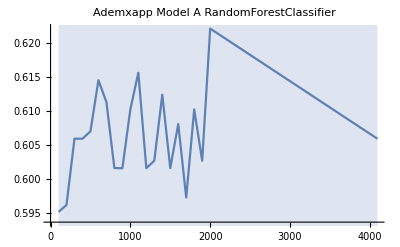
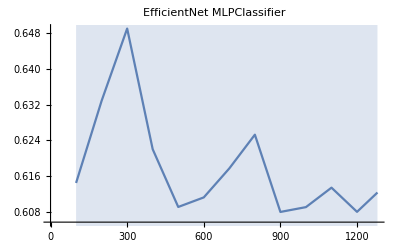
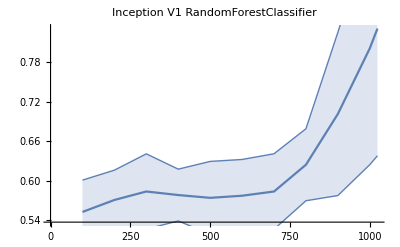
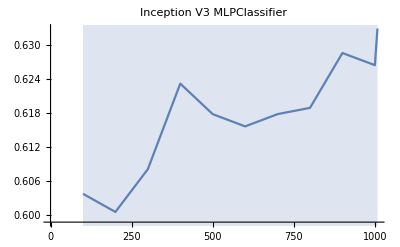
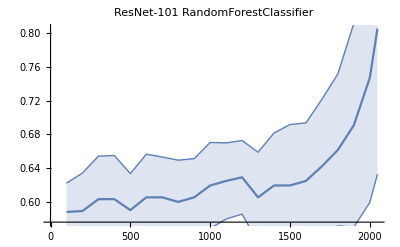
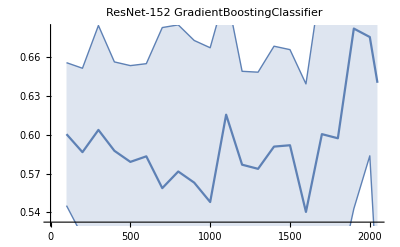
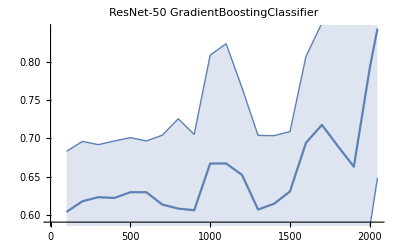
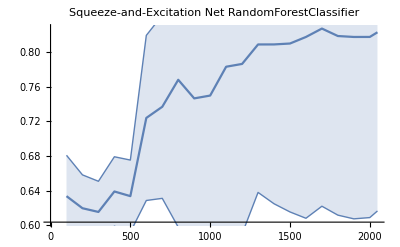

```mathematica
Module[{maxAcIdx=listArgMax[#["avg_test_accuracy"]]},
model=#["Model"]⟦maxAcIdx⟧;
csvDS=Transpose[Dataset[#][KeyDrop[{"class","type","model"}]]];
testData=csvDS[Select[#Model==model&],{#["Selected"],Around[#["avg_test_accuracy"],#["std_test_accuracy"]]}&]//Normal;
trainData=csvDS[Select[#Model==model&],{#["Selected"],Around[#["avg_train_accuracy"],#["std_train_accuracy"]]}&]//Normal;
ListLinePlot[{testData(*,trainData*)},IntervalMarkers->"Bands",PlotLabel->Column[{#["model"],model},Alignment->Center]]
]&/@Select[extractedResultsAssocs,#class=="5Class"&]
```

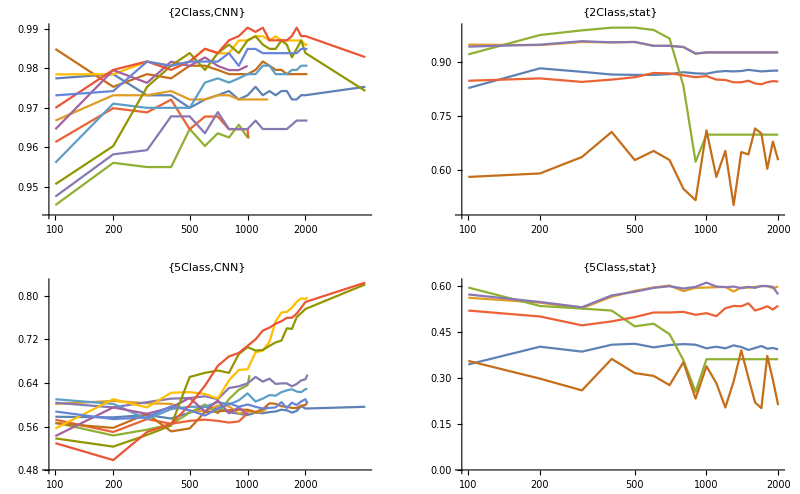

```mathematica
GraphicsGrid[Table[
ListLinePlot[Module[{maxAcIdx=listArgMax[#["avg_test_accuracy"]]},
model=(*"MLPClassifier"*)"LinearSVC";
csvDS=Transpose[Dataset[#][KeyDrop[{"class","type","model"}]]];
testData=csvDS[Select[#Model==model&],{#["Selected"],Around[#["avg_test_accuracy"],#["med_test_accuracy"]]}&]//Normal;
trainData=csvDS[Select[#Model==model&],{#["Selected"],Around[#["avg_train_accuracy"],#["std_train_accuracy"]]}&]//Normal;
testData
]&/@Select[extractedResultsAssocs,#class==class&&#type==type&],IntervalMarkers->"None",PlotRange->All,ScalingFunctions->{"Log",None},PlotLabel->{class,type}]
,{class,{"2Class","5Class"}},{type,{"CNN","stat"}}]]
```

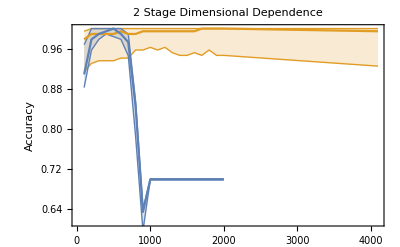
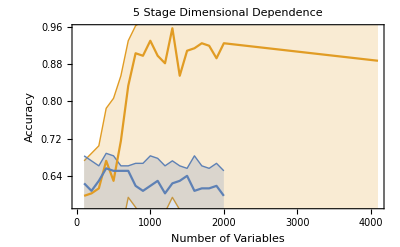

```mathematica
NameAssoc=<|"2Class"->"2 Stage","5Class"->"5 Stage"|>;
{dimPlot1,dimPlot2}=Table[
{class,mdls}=dat;
ListLinePlot[
Module[{maxAcIdx=listArgMax[#["avg_test_accuracy"]]},
model=#["Model"]⟦maxAcIdx⟧;
csvDS=Transpose[Dataset[#][KeyDrop[{"class","type","model"}]]];
testData=csvDS[Select[#Model==model&],{#["Selected"],
Around[Median[#],{Median[#]-Min[#],Max[#]-Median[#]}]&[StringReplace[#["all_test_accuracy"],{"["->"{","]"->"}"}]//ToExpression]
}&]//Normal;
trainData=csvDS[Select[#Model==model&],{#["Selected"],
Around[Median[#],{Median[#]-Min[#],Max[#]-Median[#]}]&[StringReplace[#["all_test_accuracy"],{"["->"{","]"->"}"}]//ToExpression]
}&]//Normal;
testData
]&/@Select[extractedResultsAssocs,#class==class&&MemberQ[mdls,#model]&]
,IntervalMarkers->"Bands",PlotRange->All,ScalingFunctions->{None,None},PlotLabel->(NameAssoc[class]<>" Dimensional Dependence"),Frame->True,FrameLabel->{If[class==="5Class","Number of Variables",None],"Accuracy"},FrameStyle->sty,LabelStyle->sty,PlotStyle->{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798]}]
,{dat,{{"2Class",{"VGG-19","LLE"}},{"5Class",{"VGG-19","PrincipalComponentsAnalysis"}}}}]
```

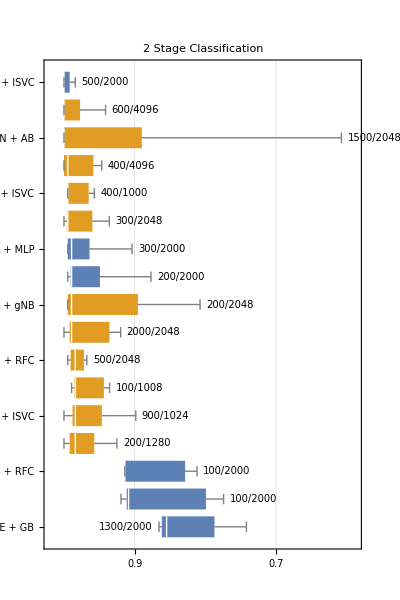
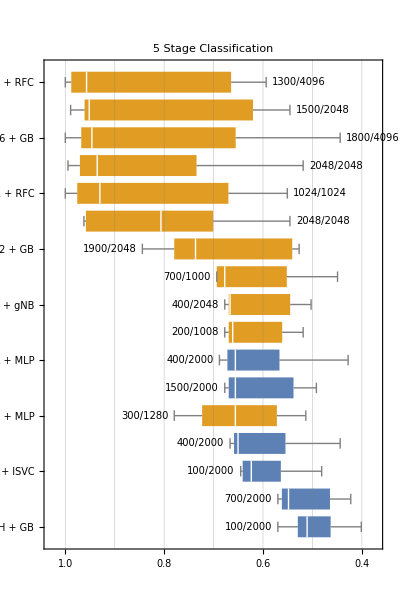
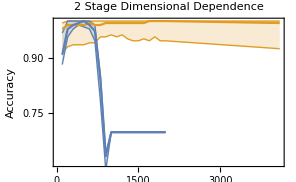
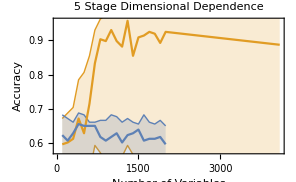
-Graphics- | -Graphics- | -Graphics-
 |  | -Graphics-

```mathematica
Style[Grid[{{twoStageResults,fiveStageResults,dimPlot1},{SpanFromAbove,SpanFromAbove,dimPlot2}},Alignment->{Left,Center}],ImageSizeMultipliers->{1,1}]
```

```mathematica
LineLegend[{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798]},{"VGG-19 + VC","LLE + LSVC"}]
```

```mathematica
LineLegend[{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798]},{"VGG-19 + RFC","PCA + MLP"}]
```

```mathematica
SwatchLegend[{clr1,clr2},{"CNN","Statistical"}]
```

```mathematica
LineLegend[{Directive[Gray,Dashed]},{"VGG-19 + VC","LLE + LSVC"}]
```

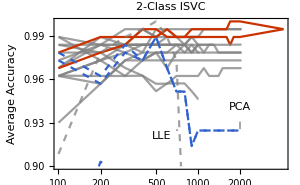

```mathematica
class="2Class";
validAssoc=Select[extractedResultsAssocs,#class==class&];
ListLinePlot[Module[{maxAcIdx=listArgMax[#["avg_test_accuracy"]]},
model="LinearSVC";
csvDS=Transpose[Dataset[#][KeyDrop[{"class","type","model"}]]];
testData=csvDS[Select[#Model==model&],{#["Selected"],#["med_test_accuracy"]}&]//Normal;
If[MemberQ[{"LLE","PCA","SEN"(*,"SE-RN-101"*)(*,"H"*)},abrvAssoc@#["model"]],
Callout[Tooltip[Select[testData,#[[2]]>=.80&],abrvAssoc@#["model"]],abrvAssoc@#["model"],
Switch[abrvAssoc@#["model"],"LLE",{700,0.925},"SEN",{2500,.99},(*"SE-RN-101",{Right,Above},*)(*"H",Above,*)_,Right],Appearance->"Balloon"(*,CalloutMarker->"CirclePoint"*)]
,
Tooltip[testData,#["model"]]]

]&/@validAssoc,IntervalMarkers->"None",PlotRange->{.9,1},PlotRangePadding->0.0001,ScalingFunctions->{"Log",None},
PlotStyle->(Directive[{If[#type=="stat",Dashed,Sequence[]],
Which[
StringContainsQ[#model,"VGG"],ColorData[112][1],
MemberQ[{"PCA","LSA","H"},abrvAssoc@#["model"]],ColorData[112][2],
(*StringContainsQ[abrvAssoc@#model,"SE"],ColorData[112][3],*)
True,Directive[{Opacity[0.75],Gray}]
]}]&/@validAssoc),
PlotLabel->"2-Class lSVC",Frame->True,FrameLabel->{If[class==="5Class","Number of Variables",None],"Average Accuracy"},LabelStyle->Black,FrameStyle->Black,ImageSize->300]
```

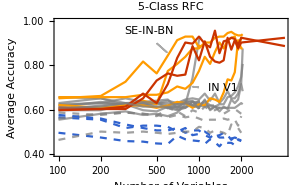

```mathematica
tickfunc[xmin_,xmax_]:=Table[{x,If[x<1,ToString[SetPrecision[x,1]]<>"0","1.00"]},{x,xmin,xmax,(xmax-xmin)/6}]

class="5Class";
validAssoc=Select[extractedResultsAssocs,#class==class&];
ListLinePlot[Module[{maxAcIdx=listArgMax[#["avg_test_accuracy"]]},
model="RandomForestClassifier";
csvDS=Transpose[Dataset[#][KeyDrop[{"class","type","model"}]]];
testData=csvDS[Select[#Model==model&],{#["Selected"],#["med_test_accuracy"]}&]//Normal;
If[MemberQ[{"IN V1","SE-IN-BN"(*,"RN-50"*)},abrvAssoc@#["model"]],
Callout[Tooltip[testData,#["model"]],abrvAssoc@#["model"],
Switch[abrvAssoc@#["model"],"SE-IN-BN",{500,0.9},(*"RN-50",{Right},*)_,{1000,0.7}],Appearance->"Balloon"(*,CalloutMarker->"CirclePoint"*)
]
,
Tooltip[testData,#["model"]]]

]&/@validAssoc,IntervalMarkers->"None",PlotRange->{{100,4000},{0.4,1}},PlotRangePadding->0.0001,ScalingFunctions->{"Log",None},
PlotStyle->(Directive[{If[#type=="stat",Dashed,Sequence[]],
Which[
StringContainsQ[#model,"VGG"],ColorData[112][1],
MemberQ[{"PCA","LSA","H"},abrvAssoc@#["model"]],ColorData[112][2],
StringContainsQ[abrvAssoc@#model,"SE"]||StringContainsQ[abrvAssoc@#model,"RNX"],ColorData[112][3],
True,Directive[{Opacity[0.75],Gray}]
]}]&/@validAssoc),
PlotLabel->"5-Class RFC",Frame->True,FrameLabel->{If[class==="5Class","Number of Variables",None],"Average Accuracy"},LabelStyle->Black,FrameStyle->Black,ImageSize->300,FrameTicks->{{tickfunc,None},{Automatic,None}}]
```

```mathematica
E^16//N
```

8.88611×10^6

```mathematica
LineLegend[ColorData[112]/@Range[3][[{1,3,2}]],{"VGG","Linear","SENet"}[[{1,3,2}]]]
```

```mathematica
LineLegend[ColorData[112]/@Range[3][[{1,2}]],{"VGG","Linear","SENet"}[[{1,2}]]]
```